```mathematica
Dist[a1_,a2_]=Sqrt[(a1[[1]]-a2[[1]])^2+(a1[[2]]-a2[[2]])^2];
InCircle[p1_,p2_,p3_,p4_]=Block[{ma,mb,xc,yc,rc},
(*Сheck that p4 in circle p1,p2,p3;
return:: {result,coords(x,y),radius}*)
ma=(p2[[2]]-p1[[2]])/(p2[[1]]-p1[[1]]);
(*Print["ma=",ma];*)
mb=(p3[[2]]-p2[[2]])/(p3[[1]]-p2[[1]]);
xc=(ma mb(p1[[2]]-p3[[2]])+ mb (p1[[1]]+p2[[1]])-ma(p2[[1]]+p3[[1]]))/(2 (mb-ma));
yc=-1/ma (xc-(p1[[1]]+p2[[1]])/2)+(p1[[2]]+p2[[2]])/2;
rc=Dist[{xc,yc},p1];
(*Print["rc=",rc"; xc=",xc,";yc=",yc];*)
res =Dist[{xc,yc},p4]<=rc;
{res,xc,yc,rc}
(*Print["Result=",res]]*)];
```

Part::partd: Part specification a1⟦1⟧ is longer than depth of object.

Part::partd: Part specification a2⟦1⟧ is longer than depth of object.

Part::partd: Part specification a1⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification p2⟦2⟧ is longer than depth of object.

Part::partd: Part specification p1⟦2⟧ is longer than depth of object.

Part::partd: Part specification p2⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
file="C:\\Users\\Yawor\\OneDrive\\Рабочий стол\\test_points_1.wdx"
```

C:\Users\Yawor\OneDrive\Рабочий стол\test_points_1.wdx

```mathematica
(*Поиск лижайших точек с доверительным радиусом {data_,r_,pc_}*)
data=Import[file];
a=0;
b=100;
c=-100;
d=100;
n=20;
inner ={};
len=Length[data];
koef =Sqrt[len /n];
pc=data[[1]];
(*Ниже вычисляется радиус и находится массив ближних точек*)
r= (Dist[{a,c},{b,d}]/koef/2);
pc=data[[1]]
(*Поиск лижайших точек с доверительным радиусом {data_,r_,pc_}*)
Do[If[Dist[pc,data[[i]]]<=r,AppendTo[inner,i],0],{i,1,Length[data],1}];
Length[inner]
```

{21.4104,70.7439}

32

32

{1002,847,540,662,1062,816,395,480,301,1190,758,535,1020,841,595,1189,1095,1249,677,467,457,528,930,1218,933,884,1010,883,629,762,1016}

31

{True,21.8168,87.0465,16.3077}

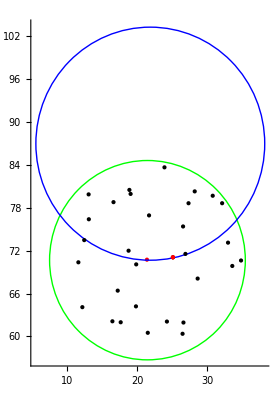

```mathematica
(*Сортировка по тангенсу*)

first={};
second={};
third={};
fourth={};
Length[inner]
data[[inner[[1]]]][[1]]+pc[[1]];
Do[
tmp1=data[[inner[[i]]]][[1]]-pc[[1]];
tmp2=data[[inner[[i]]]][[2]]-pc[[2]];
If[(tmp1)>0&&(tmp2)>0,AppendTo[first,{inner[[i]],tmp2/tmp1}],0  ];
If[tmp1<0&&tmp2>0,AppendTo[second,{inner[[i]],tmp2/tmp1}],0  ];
If[tmp1<0&&tmp2<0,AppendTo[third,{inner[[i]],tmp2/tmp1}],0  ];
If[tmp1>0&&tmp2<0,AppendTo[fourth,{inner[[i]],tmp2/tmp1}],0  ];
,{i,1,Length[inner],1}];
(*add sortby and merge*)
first=SortBy[first,Last];
second=SortBy[second,Last];
third=SortBy[third,Last];
fourth =SortBy[fourth,Last];
sortedPoints=Join[first[[All,1]],second[[All,1]],third[[All,1]],fourth[[All,1]]]
Length[sortedPoints]
(*Picture_1*)
res =InCircle[pc,data[[sortedPoints[[1]]]],data[[sortedPoints[[2]]]],data[[sortedPoints[[4]]]]]
pic2=Graphics[
{{Green,Circle[pc,r]},PointSize[Large],{Red,Point[pc]},
{Blue,Circle[{res[[2]],res[[3]]},res[[4]]]},
Map[

Point[#]&
,data[[sortedPoints]]],{ Red,Point[data[[sortedPoints[[{1,1}]]]]]}},Axes->True
]
(*Export["pic3.png",pic2]
SystemOpen["pic3.png"]*)
```

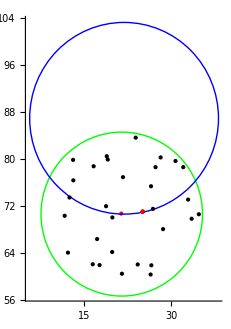

{{1,10},{10,16},{16,19},{19,24}}

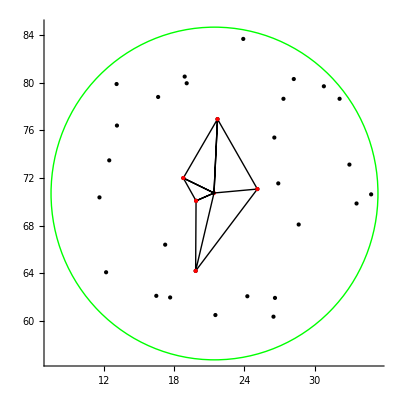

```mathematica
triangles ={};
pointtmp= 1;

p=4;(*Length[sortedPoints]//2; Последние отдельно рассмотреть надо*)
Do[(*цикл по точкам для построения треугольников*)
	f=0;
	Do[(*цикл-чекалка выполнения условия Делоне*)
	If[(j!=pointtmp)&&(j!=i) , 
		res =InCircle[pc,data[[sortedPoints[[pointtmp]]]],data[[sortedPoints[[i]]]],data[[sortedPoints[[j]]]]];
		If [res[[1]]==True,f=1]
	]		

	,{j,1,Length[sortedPoints]}];
	If[f==0,
		AppendTo[triangles,{pointtmp,i}];
		pointtmp=i];
,{i,2,Length[sortedPoints]}];



triangles (*перевести в глобальную нумерацию*)
linelist={};
Do[
AppendTo[linelist, pc];
AppendTo[linelist, data[[sortedPoints[[triangles[[i]][[1]]]]]]];
AppendTo[linelist, data[[sortedPoints[[triangles[[i]][[2]]]]]]];
AppendTo[linelist, pc];
,{i,1,Length[triangles]}]
pic4=Graphics[
{{Green,Circle[pc,r]},PointSize[Large],{Red,Point[pc]},
Line[linelist],
Line[{ data[[sortedPoints[[triangles[[1]][[1]]]]]], data[[sortedPoints[[triangles[[-1]][[2]]]]]]}],(*костыль*)

Map[

Point[#]&
,data[[sortedPoints]]],{ Red,Point[data[[sortedPoints[[{1,10,16,19,24}]]]]]}},Axes->True
]
```

```mathematica
{{21.410418670043597,70.7438653452709},{25.11291887635194,71.07537909841881},{21.709245896018693,76.94001307949583},{21.410418670043597,70.7438653452709},{21.410418670043597,70.7438653452709},{21.709245896018693,76.94001307949583},{18.791481942490947,71.9995392050021},{21.410418670043597,70.7438653452709},{21.410418670043597,70.7438653452709},{18.791481942490947,71.99953920500215},{19.879015358231918,70.08596776227711},{21.410418670043597,70.7438653452709},{21.410418670043597,70.7438653452709},{19.879015358231918,70.08596776227711},{19.84396718628754,64.21062136968513},{21.410418670043597,70.7438653452709}}
```

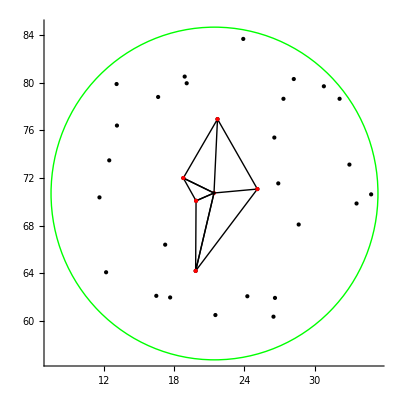

```mathematica
pic4=Graphics[
{{Green,Circle[pc,r]},PointSize[Large],{Red,Point[pc]},
Line[{pc,data[[sortedPoints[[1]]]],data[[sortedPoints[[10]]]], pc, data[[sortedPoints[[16]]]], data[[sortedPoints[[10]]]]}],
Line[{pc,data[[sortedPoints[[16]]]],data[[sortedPoints[[19]]]],pc}],
Line[{pc,data[[sortedPoints[[24]]]],data[[sortedPoints[[19]]]],pc}],
Line[{pc,data[[sortedPoints[[24]]]],data[[sortedPoints[[1]]]]}],
Map[

Point[#]&
,data[[sortedPoints]]],{ Red,Point[data[[sortedPoints[[{1,10,16,19,24}]]]]]}},Axes->True
]
(*Export["pic4.png",pic4]
SystemOpen["pic4.png"]*)
```